```mathematica
data="[[111.5406494140625, 109.67989349365234, 110.9552993774414, 108.75184631347656, 114.32801055908203, 112.37532043457031, 112.61180877685547, 109.82459259033203, 111.62741088867188, 113.04523468017578, 119.81019592285156, 112.51264953613281, 115.0881118774414, 109.69331359863281, 110.81085968017578, 110.8729248046875, 110.69241333007812, 107.08590698242188, 113.44341278076172, 114.39774322509766, 108.85160064697266, 109.6169662475586, 111.40321350097656, 114.26602935791016, 112.2437744140625, 109.07392120361328, 109.16975402832031, 107.95294189453125, 110.02708435058594, 110.11180114746094, 113.12081146240234, 109.57000732421875, 108.73204803466797, 108.83275604248047, 108.76665496826172, 108.86824035644531, 110.09841918945312, 110.09121704101562, 109.96764373779297, 107.59036254882812], [72.22057342529297, 74.84281921386719, 64.8193130493164, 67.5648422241211, 70.52532196044922, 67.50662231445312, 78.20569610595703, 65.0877914428711, 72.6133041381836, 89.07587432861328, 65.60433197021484, 67.70660400390625, 68.00096130371094, 64.71697235107422, 74.38811492919922, 65.38185119628906, 71.3641128540039, 85.97294616699219, 101.23851776123047, 69.98480987548828, 67.02584838867188, 88.22820281982422, 69.56531524658203, 65.07118225097656, 68.01061248779297, 65.0535888671875, 65.8294906616211, 88.68376159667969, 67.74127197265625, 94.36705780029297, 75.68016052246094, 67.24849700927734, 78.528076171875, 65.8861083984375, 88.3489761352539, 69.08977508544922, 90.478759765625, 75.8103256225586, 90.41149139404297, 75.02064514160156], [117.2233657836914, 125.0372543334961, 109.6888427734375, 111.49925231933594, 110.75116729736328, 109.9981918334961, 113.56477355957031, 116.72833251953125, 111.61629486083984, 113.84720611572266, 110.78685760498047, 116.90801239013672, 111.10768127441406, 111.54426574707031, 110.24624633789062, 112.24322509765625, 111.87388610839844, 110.84176635742188, 109.61512756347656, 121.33712005615234, 121.27110290527344, 116.41744232177734, 111.23687744140625, 109.80029296875, 110.80962371826172, 111.2088623046875, 111.039306640625, 112.98529815673828, 111.67973327636719, 110.54353332519531, 115.41927337646484, 110.6647720336914, 111.65760803222656, 109.76363372802734, 112.39330291748047, 113.09862518310547, 116.54730987548828, 124.3017807006836, 112.80619049072266, 112.32218170166016], [92.33406066894531, 88.81129455566406, 94.4762191772461, 100.27243041992188, 80.93855285644531, 91.24212646484375, 89.04067993164062, 83.60453033447266, 78.21076202392578, 76.72676849365234, 94.74561309814453, 93.61354064941406, 99.22700500488281, 92.38829803466797, 91.83456420898438, 81.12528991699219, 75.7118911743164, 91.066162109375, 97.93385314941406, 75.10762023925781, 86.1317138671875, 94.1889877319336, 81.2527847290039, 92.65775299072266, 89.99980163574219, 94.95279693603516, 85.70132446289062, 91.04065704345703, 94.31106567382812, 91.8089599609375, 80.6400375366211, 86.25846099853516, 89.62185668945312, 89.74605560302734, 102.40279388427734, 99.4928207397461, 80.06448364257812, 89.1058349609375, 90.80117797851562, 96.17495727539062], [88.75968933105469, 81.18256378173828, 91.36408996582031, 74.2540283203125, 81.22371673583984, 77.83499908447266, 81.48778533935547, 99.1550521850586, 82.49799346923828, 102.99117279052734, 76.14407348632812, 85.31900024414062, 80.57069396972656, 96.19850158691406, 83.41686248779297, 93.59716033935547, 105.33768463134766, 77.3218765258789, 89.48416137695312, 72.47371673583984, 90.8436279296875, 87.32013702392578, 94.12059783935547, 88.99519348144531, 85.32447052001953, 88.8046646118164, 93.7333755493164, 74.50273132324219, 78.92732238769531, 93.85636901855469, 81.11354064941406, 73.4670181274414, 89.14464569091797, 91.92333221435547, 88.14851379394531, 81.90740966796875, 110.52220916748047, 92.70999908447266, 94.61332702636719, 82.19569396972656]]";
```

```mathematica
ndata=ToExpression@StringReplace[data,{"["->"{","]"->"}"}];
```

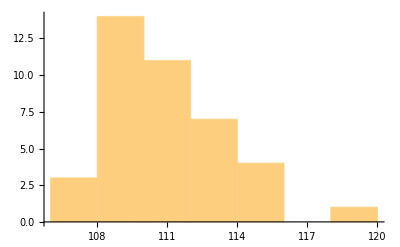
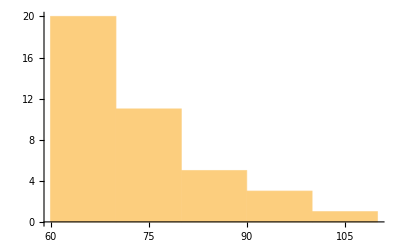
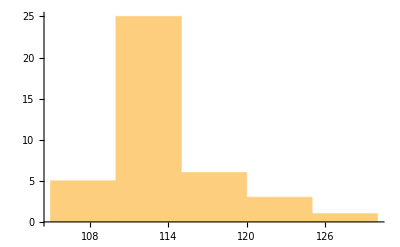
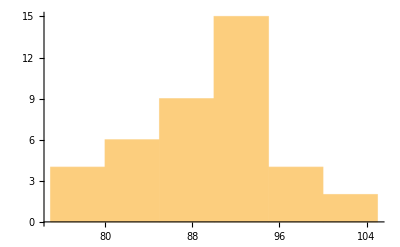
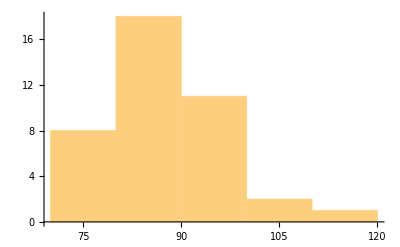

```mathematica
Histogram/@ndata
```

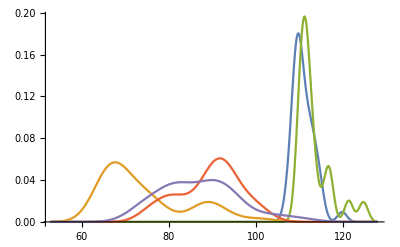

```mathematica
SmoothHistogram[ndata,PlotRange->All]
```